```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[If[ii≥1,n=temp[[ii]]-1;
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],BW[w,wr,Γ,δbg,const,shift,shift2],{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->20000,Method->"LevenbergMarquardt"],{i,Length[hwhmi]}]];,{ii,len}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,1,Length[res]}];Export["spectraldata/Npartscan/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])(const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,1,Length[res]}];Export["spectraldata/Npartscan/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Npartscan/"<>ToString[res]<>".dat"];
```

## Npart scan

```mathematica
ccdata[0]=Import["spectraldata/Npartscan/swccNpart0spectra.dat"];
ccdata[1]=Import["spectraldata/Npartscan/swccNpart1spectra.dat"];
ccdata[2]=Import["spectraldata/Npartscan/swccNpart2spectra.dat"];
ccdata[3]=Import["spectraldata/Npartscan/swccNpart3spectra.dat"];
ccdata[4]=Import["spectraldata/Npartscan/swccNpart4spectra.dat"];
ccdata[5]=Import["spectraldata/Npartscan/swccNpart5spectra.dat"];
ccdata[6]=Import["spectraldata/Npartscan/swccNpart6spectra.dat"];
ccdata[7]=Import["spectraldata/Npartscan/swccNpart7spectra.dat"];
ccdata[8]=Import["spectraldata/Npartscan/swccNpart8spectra.dat"];
ccdata[9]=Import["spectraldata/Npartscan/swccNpart9spectra.dat"];
ccdata[10]=Import["spectraldata/Npartscan/swccNpart10spectra.dat"];
```

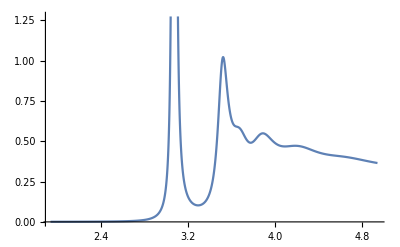

```mathematica
ListPlot[ccdata[0],Joined->True]
```

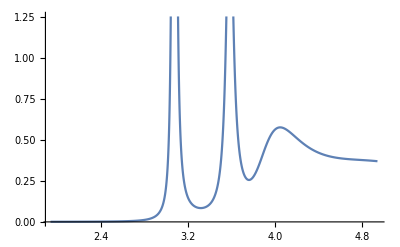

```mathematica
ListPlot[ccdata[10],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodel]
fitnew[ccdata,ccmodel,11];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,gfitcc,areafitcc,cfitcc,dfitcc,sfitcc,s2fitcc,wrfitccu,gfitccu,areafitccu,cfitccu,dfitccu,sfitccu,s2fitccu,wrfitccl,gfitccl,areafitccl,cfitccl,dfitccl,sfitccl,s2fitccl];
store[wr,wrfitcc,ccmodel];
store[Γ,gfitcc,ccmodel];
store[const,cfitcc,ccmodel];
store[δbg,dfitcc,ccmodel];
store[shift,sfitcc,ccmodel];
store[shift2,s2fitcc,ccmodel];
storearea[areafitcc,ccmodel];
```

```mathematica
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitccu,ccmodelu];
store[const,cfitccu,ccmodelu];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitccu,ccmodelu];
store[wr,wrfitccl,ccmodell];
store[Γ,gfitccl,ccmodell];
store[const,cfitccl,ccmodell];
store[δbg,dfitccl,ccmodell];
store[shift,sfitccl,ccmodell];
store[shift2,s2fitccl,ccmodell];
storearea[areafitccl,ccmodell];
```

### Import previous results

```mathematica
import[wrfitcc];
import[gfitcc];
import[cfitcc];
import[dfitcc];
import[sfitcc];
import[s2fitcc];
import[areafitcc];
import[wrfitccu];
import[gfitccu];
import[cfitccu];
import[dfitccu];
import[sfitccu];
import[s2fitccu];
import[areafitccu];
import[wrfitccl];
import[gfitccl];
import[cfitccl];
import[dfitccl];
import[sfitccl];
import[s2fitccl];
import[areafitccl];
```

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,2,1}]
```

### Dilepton ratio

```mathematica
Tmu={0.15485899763908725,0.0016486158206386965};
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
nBi[w_,T_]:=NIntegrate[p^2 nB[√(w^2+p^2),T] w/(√(w^2+p^2)),{p,0,∞}];
Rll[T_,i_,ii_]:=NIntegrate[BWi[w,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]]nB[√(w^2+p^2),T](p^2 w)/(√(w^2+p^2)),{w,0,∞},{p,0,∞},WorkingPrecision->10];
```

```mathematica
R0=ConstantArray[0,Length[wrfitcc]];
Do[If[Length[wrfitcc[[ii]]]==2,R0[[ii]]={(ii-1),Emfactor (areafitcc[[ii,2]]nBi[wrfitcc[[ii,2]],Tmu[[1]]])/(areafitcc[[ii,1]]nBi[wrfitcc[[ii,1]],Tmu[[1]]])}],{ii,Length[R0]}];
R0=DeleteCases[R0,0];
```

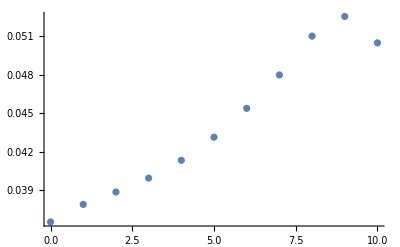

```mathematica
ListPlot[R0]
```

```mathematica
NpartTab={{0.,384.7728519855433},{0.1,384.7263508701577},{0.2,384.5867433339151},{0.30000000000000004,384.3535394578965},{0.4,384.02594565602163},{0.5,383.6030048119073},{0.6000000000000001,383.0834676075236},{0.7000000000000001,382.4659696270717},{0.8,381.7489558324545},{0.9,380.93117913568767},{1.,380.01087950465956},{1.1,378.98676226961925},{1.2000000000000002,377.8575748742697},{1.3,376.622225263531},{1.4000000000000001,375.28000886743274},{1.5,373.8303130502087},{1.6,372.2728187006724},{1.7000000000000002,370.60769757912675},{1.8,368.8352889382444},{1.9000000000000001,366.95629143639457},{2.,364.97171797644626},{2.5,353.5198092012767},{3.,339.72251781821217},{3.5,323.92313277377315},{4.,306.4940051979294},{4.5,287.795842564727},{5.,268.16023347141555},{5.5,247.88638442775186},{6.,227.243923707622},{6.5,206.4776066634324},{7.,185.81195116011278},{7.5,165.45541223291002},{8.,145.6033786036931},{8.5,126.44070552220617},{9.,108.14359555228016},{9.5,90.881014038979},{10.,74.81561760560234},{10.5,60.104052653777565},{11.,46.89599320570524},{11.5,35.330374594729854},{12.,25.525454683360376},{12.1,23.783558429341433},{12.2,22.115699166070954},{12.299999999999999,20.522059344908953},{12.4,19.002661320913223},{12.5,17.557367904174736},{12.6,16.18585470928035},{12.7,14.887601920990983},{12.799999999999999,13.661881915278878},{12.9,12.507749062472968},{13.,11.424035016507377},{13.1,10.409342501594857},{13.2,9.462049597192294},{13.3,8.58031380966126},{13.4,7.76208256353183},{13.5,7.005107523572185},{13.6,6.306963877248374},{13.7,5.6650729591888185},{13.8,5.076727884087696},{13.9,4.539121679919598},{14.,4.049377185508544},{14.1,3.6045768793511743},{14.2,3.2017925201030866},{14.3,2.838113857708717},{14.4,2.5106749094015037},{14.5,2.2166973298629724},{14.6,1.9534340759438225},{14.7,1.718302846970007},{14.8,1.508823203607699},{14.9,1.3226467365184216},{15.,1.157564648905781}};
Npartinter=Interpolation[NpartTab];
```

```mathematica
R0=ConstantArray[0,Length[wrfitcc]];
Do[If[Length[wrfitcc[[ii]]]==2,R0[[ii]]={Npartinter[ii-1],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tmu[[1]]])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tmu[[1]]])}],{ii,Length[R0]}];
R0=DeleteCases[R0,0];
```

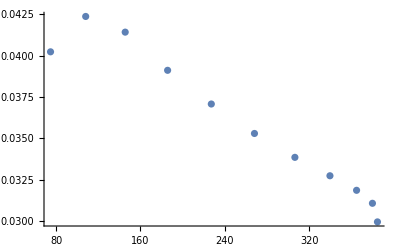

```mathematica
ListPlot[R0]
```